```mathematica
Try using :http://www.wolfram.com/mathematica/new-in-9/advanced-hybrid-and-differential-algebraic-equations/billiard-balls.html

Make initialization cells
Simplify code.
```

```mathematica
WhenEvent   
or look up Ray-casting
```

### Use Friction To control position of 2 robots.

Assume friction is inifinite:  a robot touching top wall wil not move in x direction.
step 1 : manipulate that can set initial and final position of 2 robots
step 2: simulate the effect of control actions on the robots.
function : achieveDesiredXspacing
function : achieveDesiredYspacing[[
logic to choose which function to use
simulate the inputs.

```mathematica
p={{0,0},{-3/2,3/4},{-1,0}}
p[[0]]
```

{{0,0},{-3/2,3/4},{-1,0}}

List

```mathematica
Length[ {{0,0},{1/4,1/4},{1/4,-1/4},{-1/4,-1/4}}]
```

4

```mathematica
ApplyMove[{1,0},{0,1}]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

If[Indeterminate≤1&&Indeterminate≤1,(1/2 (Plus@@#1⟦1⟧-Subtract@@#1⟦1⟧ Last[#1⟦2⟧])&)[{First[{{{1,0},{1,1}},{{1,0},{1,1}}}],{Indeterminate,Indeterminate}}],False]

```mathematica
segsegintersection[lines_]:=Quiet[Module[{md=Subtract@@(Plus@@#&/@lines),sub=Subtract@@#&/@lines,det},
(* INPUTS: a list of lines   {{line1}, {line2}}, where line = {{x0,y0},{x2,y1}}
returns {x,y} intersection point if *)
det=-Det[sub];
If[And@@(Abs[#]≤1&/@#),(Plus@@#⟦1⟧-Subtract@@#⟦1⟧ Last@#⟦2⟧)/2&@{First@lines,#},False]&@(Det[{#⟦1⟧,md}]/det&/@({#,Reverse@#}&@sub))],General::infy];
FindIntersectionOfsegmentWithWalls[seg_,walls_]:=First[Select[segsegintersection[#]&/@Table[{seg,edge},{edge,walls}],#=!=False&]];

moveParticleInWalls[pos_,move_]:=Module[{x = pos⟦1⟧,y = pos⟦2⟧,moveApplied= pos+move,newPos,
walls = {{{0,0},{0,1}},
 {{0,1},{1,1}},
 {{1,1},{1,0}},
 {{1,0},{0,0}}}
},
(*move:  {Δx, Δy},
walls = list of line segments
pos = {x, y} position*)
If[  (x≠ 1 && y≠ 1&&x≠ 0 && y≠ 0 )(*not touching wall*),
(*true*)
If[ (moveApplied⟦1⟧< 1 && moveApplied⟦1⟧>0 && moveApplied⟦2⟧ <1&& moveApplied⟦2⟧>0 ),
(*apply move*)
newPos = pos+move,
(*stop movement*)
(*newPos = pos+move*)
newPos =FindIntersectionOfsegmentWithWalls[{pos,moveApplied},walls]
],
(*we are touching the walls.  Which wall?*)
newPos=If[Abs[move⟦1⟧]>0|| Abs[move⟦2⟧]>0 (*skip zero movements*),Module[
{αDes ,(*-π,π*)
moveOK },
moveOK = True;
αDes = ArcTan[move⟦1⟧,move⟦2⟧];
If[x == 0 && Abs[αDes]≥ π/2-1/1000, moveOK = False];
If[x == 1 && Abs[αDes]≤ π/2+1/1000 , moveOK = False];
If[y == 1 &&( αDes≥ -1/1000 || αDes ≤ -π+1/1000 ), moveOK = False];
If[y == 0 && (αDes≤ 1/1000 || αDes ≥  π-1/1000), moveOK = False];
If[moveOK,pos+move,pos]
], pos]
]]
```

```mathematica
{αDes=ArcTan[{-0.02400000000000002,0.}⟦1⟧,{-0.02400000000000002,0.}⟦2⟧],moveOK=True}
```

{3.14159,True}

```mathematica
achieveDesiredXspacing[ps1_,ps2_,pe1_,pe2_]:=Module[{Δe , Δx , L , 
currPosTop, currPosBottom,Δr, moves,poses, endPosTop, endPosBottom, myϵ = 1/1000
},

(*determine which point is highest*)
If[ps1⟦2⟧>ps2⟦2⟧, 
currPosTop = ps1; currPosBottom=ps2;endPosTop = pe1; endPosBottom= pe2;,
currPosTop = ps2; currPosBottom=ps1; endPosTop = pe2; endPosBottom= pe1;
];
Δe = endPosTop⟦1⟧-endPosBottom⟦1⟧; (*desired difference*)
Δx = currPosTop⟦1⟧ - currPosBottom⟦1⟧; (*current distance*)
moves = {{0,0}};  (*list of commanded moves, in form {Δx, Δy}*)
L= 1;  (*size of workspace*)

(*Print[StringForm["ps1 = ``, ps2 = ``, pe1= ``,pe2 = ``, Δe = ``,Δx = ``",ps1,ps2,pe1,pe2,Δe,Δx ]];*)
(*For[i=1,i≤2,i++,*)
If[Δx==Δe, 
Δr = {endPosTop⟦1⟧ - currPosTop⟦1⟧ , endPosTop⟦2⟧ - currPosTop⟦2⟧ };
AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr; 
Return[moves]]; (*base case -- end the recursion*)

 Δr = {If[ Δe < 0,  (*right*)
(*1. move almost to right wall*)
 L - Max[currPosTop⟦1⟧ , currPosBottom⟦1⟧]-myϵ,(*1. move almost to left wall*) -Min[currPosTop⟦1⟧ , currPosBottom⟦1⟧]+myϵ],0};
AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr; 
(*2. move to bottom*)
Δr={ 0, -currPosBottom⟦2⟧};

AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr; 
(*3. drag sideways to left or right*)

Δr = {If[Δe-Δx >0 ,Min[Abs[Δe-Δx], L- currPosTop⟦1⟧],-Min[Abs[Δe-Δx], currPosTop⟦1⟧]],0};

AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr; 
(*4. move up*)
Δr={ 0,myϵ};
AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr; 

Δx = currPosTop⟦1⟧ - currPosBottom⟦1⟧;
(*If[Δx==Δe, Return[moves], Return[Join[moves,achieveDesiredXspacing[currPosTop,currPosBottom, pe1,pe2]]]];*)
Δr = endPosTop- currPosTop;(*{endPosTop⟦1⟧- currPosTop⟦1⟧,0} ;*)
AppendTo[moves , Δr];currPosTop+=Δr; currPosBottom+=Δr;
(*poses = {currPosTop, currPosBottom};
Return[moves,poses]*)
Return[moves];
]
```

```mathematica
achieveDesiredYspacing[ps1_,ps2_,pe1_,pe2_]:=Module[{Δe , Δy , L , 
currPosRight, currPosLeft,Δr, moves, endPosRight, endPosLeft, myϵ = 1/1000
},

(*determine which point is rightest*)
If[ps1⟦1⟧>ps2⟦1⟧, 
currPosRight = ps1; currPosLeft=ps2;endPosRight = pe1; endPosLeft= pe2;,
currPosRight = ps2; currPosLeft=ps1; endPosRight = pe2; endPosLeft= pe1;
];
Δe = endPosRight⟦2⟧-endPosLeft⟦2⟧; (*desired difference*)
Δy = currPosRight⟦2⟧ - currPosLeft⟦2⟧; (*current distance*)
moves = {{0,0}};  (*list of commanded moves, in form {Δx, Δy}*)
L= 1;  (*size of workspace*)

(*Print[StringForm["ps1 = ``, ps2 = ``, pe1= ``,pe2 = ``, Δe = ``,Δx = ``",ps1,ps2,pe1,pe2,Δe,Δx ]];*)
(*For[i=1,i≤2,i++,*)
If[Δy==Δe, 
Δr = endPosRight- currPosRight;
AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr; 
Return[moves]]; (*base case -- end the recursion*)

 Δr = {0, If[ Δe < 0,  (*right*)
(*1. move almost to up wall*)
 L - Max[currPosRight⟦2⟧ , currPosLeft⟦2⟧]-myϵ,(*1. move almost to down wall*) -Min[currPosRight⟦2⟧ , currPosLeft⟦2⟧]+myϵ]};
AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr; 
(*2. move to left*)
Δr={ -currPosLeft⟦1⟧,0};

AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr; 
(*3. drag sideways to left or right*)

Δr = {0,If[Δe-Δy >0 ,Min[Abs[Δe-Δy], L- currPosRight⟦2⟧],-Min[Abs[Δe-Δy], currPosRight⟦2⟧]]};

AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr; 
(*4. move right*)
Δr={ myϵ,0};
AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr; 

(*Δy = currPosRight⟦2⟧ - currPosLeft⟦2⟧;*)
(*If[Δx==Δe, Return[moves], Return[Join[moves,achieveDesiredXspacing[currPosTop,currPosBottom, pe1,pe2]]]];*)
Δr = endPosRight -  currPosRight;
AppendTo[moves , Δr];currPosRight+=Δr; currPosLeft+=Δr;
Return[moves]
]
```

```mathematica
ArcTan[{-0.28,0.}⟦1⟧,{-0.28,0.}⟦2⟧]
```

3.14159

```mathematica
ApplyMove[p_,mv_]:=Module[{inter},

If[mv=={0,0},p,inter = Select[segsegintersection[#]&/@Table[{{p,p+mv},edge},{edge, {{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{0,0}},{{0,0},{1,0}}}}],#=!=False&];
If[Length[inter]<1,p+mv,inter⟦1⟧]
]]

(*If [ Abs[p⟦1⟧+mv⟦1⟧]<1 &&  Abs[p⟦2⟧+mv⟦2⟧]<1,p+mv,
p+mv*Min[{If[ (1-p⟦1⟧)/mv⟦1⟧>0,(1-p⟦1⟧)/mv⟦1⟧,∞],If[ (-1-p⟦1⟧)/mv⟦1⟧>0,(-1-p⟦1⟧)/mv⟦1⟧,∞],If[ (1-p⟦2⟧)/mv⟦2⟧>0,(1-p⟦2⟧)/mv⟦2⟧,∞],If[(-1-p⟦2⟧)/mv⟦2⟧>0,(-1-p⟦2⟧)/mv⟦2⟧,∞]}]

];*)
(*find intersection of of line from p to p+mv.  Crop move at this point*)

Manipulate[Module[{path,pathY, pm1,pm2,pmpast1, pmpast2, mv,Δxy ,path1,path2,Δsx, Δex, Δsy,Δey, psy,result, pss1, pss2},
(*path= achieveDesiredSpacing[ps1,ps2,pe1,pe2];*)
Δsx = ps1⟦1⟧- ps2⟦1⟧;
Δsy = ps1⟦2⟧- ps2⟦2⟧;
Δex= pe1⟦1⟧-pe2⟦1⟧;
Δey= pe1⟦2⟧-pe2⟦2⟧;

(*result= achieveDesiredXspacing[ps1,ps2,pe1,pe2];
Print[result];
path = result⟦1⟧;
psy = result⟦2⟧;
Print[psy];
pss1 = psy⟦1⟧;
pss2 = psy⟦2⟧;
pathY = achieveDesiredYspacing[pss1,pss2, pe1,pe2];
path = Join[path,pathY];*)

path = achieveDesiredXspacing[ps1,ps2,pe1,pe2];
If[ps1⟦2⟧>ps2⟦2⟧,
lastPos= pe2;
psy = pe1;
lastPos⟦2⟧ = pe2⟦2⟧+Δey -Δsy;
pathY = achieveDesiredYspacing[psy,lastPos, pe1,pe2];
,
lastPos= pe1;
psy = pe2;
lastPos⟦2⟧ = pe1⟦2⟧-Δey +Δsy;
pathY = achieveDesiredYspacing[lastPos,psy, pe1,pe2];
];
path = Join[path,pathY];


(*if[Δsy>ps2⟦2⟧,
path = achieveDesiredXspacing[ps1,ps2,pe1,pe2];
If[ps1⟦1⟧>ps2⟦1⟧,
lastPos= pe2;
lastPos⟦2⟧ = pe2⟦2⟧+Δey -Δsy;,lastPos= pe1;
lastPos⟦2⟧ = pe1⟦2⟧-Δey +Δsy;
];
pathY = achieveDesiredYspacing[pe1,lastPos, pe1,pe2];
path = Join[path,pathY];,
path = achieveDesiredYspacing[ps1,ps2,pe1,pe2];
If[ps1⟦1⟧>ps2⟦1⟧,
lastPos= pe2;
lastPos⟦2⟧ = pe2⟦2⟧+Δey -Δsy;,lastPos= pe1;
lastPos⟦2⟧ = pe1⟦2⟧-Δey +Δsy;
];
pathY = achieveDesiredXspacing[pe1,lastPos, pe1,pe2];
path = Join[path,pathY];

];*)
(*{{0,0},{.5,1},{-.2,-.8},{-.6,.3}};*)

Graphics[{
Black, Rectangle[-0.1{1,1},1.1{1,1}],
White, Rectangle[{0,0},{1,1}],
PointSize[Large],

Blue,{ Dashed,Line[{ps1,pe1}]},Point@ps1,Circle[pe1,1/20],
Magenta,{ Dashed,Line[{ps2,pe2}]},Point@ps2, Circle[pe2,1/20],
desiredΔx = (pe1⟦1⟧-ps1⟦1⟧)-(pe2⟦1⟧-ps2⟦1⟧);
Δxy = {0,0};
pm1 = ps1; (*pm1 = the position of the particle after the movement sequence*)
pm2 = ps2;
path1 = {pm1};
pmpast1 = {pm1};
path2 = {pm2};
pmpast2 = {pm2};
For[i=1,i<=progress*(Length[path]-1),i++,
mv = path⟦i+1⟧;
pmpast1 = {pm1};
pmpast2 = {pm2};
pm1=moveParticleInWalls[pm1,mv];
pm2=moveParticleInWalls[pm2,mv];

AppendTo[path1,pm1];
AppendTo[path2,pm2];
AppendTo[pmpast1,pm1];
AppendTo[pmpast2,pm2];
Arrow[pmpast1];
Arrow[pmpast2];
Δxy =Δxy +mv];
If[i<Length[path],
mv =  FractionalPart[progress*(Length[path]-1)]*path⟦2+Floor[progress*(Length[path]-1)]⟧;
Δxy  =Δxy +mv;
Line[{mv,Δxy +mv}];
pm1=moveParticleInWalls[pm1,mv];
pm2=moveParticleInWalls[pm2,mv];
Point@{pm1 };
Arrow[pmpast1];
Arrow[pmpast2];
Arrow[path1];
Arrow[path2];
AppendTo[path1,pm1];
AppendTo[path2,pm2];

];

Blue,Point@{pm1 },
Arrow[path1],
Magenta, Point@{pm2},
Arrow[path2]
}]],
{progress,Slider,Appearance->"Labeled"},
{{ps1,{1/3,1/8}},{-1,-1},{1,1},Locator},
{{ps2,{2/3,1/4}},{-1,-1},{1,1},Locator},
{{pe1,{1/8,1/7}},{-1,-1},{1,1},Locator},
{{pe2,{1/5,1/9}},{-1,-1},{1,1},Locator}

]
```

```mathematica
(*TODO: Correct this part of the code for doing the right move
1)X coordinate
2)Y and X together.
*)
 achieveDesiredXspacing2[ps1_,ps2_,pe1_,pe2_]:=Module[{moves,
currPosTop,currPosBottom,dir,Ydest,Δxy,distPossibleToMove,
desiredΔx
},
desiredΔx = (pe1⟦1⟧-ps1⟦1⟧)-(pe2⟦1⟧-ps2⟦1⟧);
moves = {{0,0}};
(*determine which point is highest*)
If[ps1⟦2⟧>ps2⟦2⟧,  currPosTop = ps1; currPosBottom=ps2;,
currPosTop = ps2; currPosBottom=ps1;desiredΔx=-desiredΔx;
];

If[desiredΔx==0, Return[moves]];
 dir = Sign[desiredΔx];
(*gives a sequnce of moves: {{Subscript[Δx, 1],Subscript[Δy, 1]},{Subscript[Δx, 2],Subscript[Δy, 2]},...,{Subscript[Δx, n],Subscript[Δy, n]}} that should be *)
Ydest = If[Abs[1-currPosTop⟦2⟧ ] < Abs[-1- currPosBottom⟦2⟧ ] ,1,-1];
(*move to top, then drag along top edge*)
Δxy = {dir*1,Ydest}-currPosTop;
AppendTo[moves,Δxy ];
currPosTop = currPosTop+Δxy;
currPosBottom = currPosTop+Δxy;

AppendTo[moves,{desiredΔx,0} ];
(*move to bottom, then drag along bottom edge*)
moves
]
```

```mathematica
(*achieveDesiredXspacing[ps1_,ps2_,pe1_,pe2_]:=Module[{Δe , Δx , L ,
currPosTop, currPosBottom,Δr, moves, endPosTop, endPosBottom
},
(*determine which point is highest*)
If[ps1⟦2⟧>ps2⟦2⟧,  currPosTop = ps1; currPosBottom=ps2;endPosTop = pe1; endPosBottom= pe2;,
currPosTop = ps2; currPosBottom=ps1; endPosTop = pe2; endPosBottom= pe1;
];
Δe = endPosTop⟦1⟧-endPosBottom⟦1⟧;
Δx = currPosTop⟦1⟧ - currPosBottom⟦1⟧;
moves = {{0,0}};
L= 1;


If[Δx==Δe, Return[moves]];
If[L-currPosBottom⟦1⟧ < Δe,  Δr = {L-Δe - currPosBottom⟦1⟧, 0}, Δr = {0,0}];
AppendTo[moves , Δr ];
currPosTop = currPosTop+Δr;
currPosBottom = currPosBottom+Δr;
Δr = {0,-currPosBottom⟦2⟧};
AppendTo[moves, Δr];
currPosTop = currPosTop+Δr;
currPosBottom = currPosBottom+Δr;
Δr = {Δe - Δx,0};
AppendTo[moves, Δr ];
currPosTop = currPosTop+Δr;
currPosBottom = currPosBottom+Δr;
moves
]*)
```

```mathematica
Sign[-3.6]
```

-1

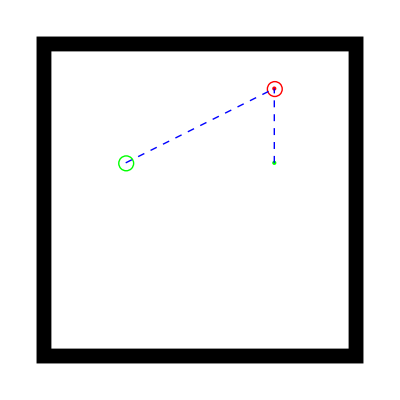

{{0,0},{501/1000,0},{0,-1/4},{999/1000,0},{0,1/1000},{-1/2,749/1000}}

```mathematica
ps1 =  {1/2,1/4};
ps2={-1/2,1/4};
pe1={1/2,3/4};
pe2={1/2,3/4};
Graphics[{
Black, Rectangle[1.1{-1,-1},1.1{1,1}],
White, Rectangle[{-1,-1},{1,1}],
PointSize[Large],
Green,Point@ps1,Circle[ps2,1/20],
Red,Point@pe1,Circle[pe2,1/20],
Blue,{ Dashed,Line[{ps1,pe1}],Line[{ps2,pe2}]},
desiredΔx = (pe1⟦1⟧-ps1⟦1⟧)-(pe2⟦1⟧-ps2⟦1⟧);
}]
achieveDesiredXspacing[ps1,ps2,pe1,pe2]
```